```mathematica
Clear[verticesOfSimplex];
Clear[configurationAdd];
Clear[configurationMinus];
Clear[partial];
Clear[hasEmptyIntersection];

(*Subscript[Z, n] excitation while moving operators are (dim)-simplex*)
types=1;
n={2,2,2};
dim={2,2,2};

(*Part1: data of complex*)
(*in a extended complex, there is a simplex of dimension=-1
simplex[-1]={1};
boundaryOfSimplex[simplexID_,0]:={1};

(*data of F-symbol(triangle)*)
simplex[0]={1,2,3};
simplex[1]={1,2,3};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={2,3};
boundaryOfSimplex[3,1]={1,3};*)


(*Data of tetrahedra in 2D: T-junction,...
simplex[0]={1,2,3,4};
simplex[1]={1,2,3,4,5,6};
simplex[2]={1,2,3,4};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={1,3};
boundaryOfSimplex[3,1]={1,4};
boundaryOfSimplex[4,1]={2,3};
boundaryOfSimplex[5,1]={2,4};
boundaryOfSimplex[6,1]={3,4};
boundaryOfSimplex[1,2]={1,2,4};
boundaryOfSimplex[2,2]={1,3,5};
boundaryOfSimplex[3,2]={2,3,6};
boundaryOfSimplex[4,2]={4,5,6};*)


(* centered tetrahedron, data of fermionic loops&membrane in 3D*)
(* Warning: labels and orders of these data cannot be changed!*)
simplex[0]={1,2,3,4,5};
simplex[1]={1,2,3,4,5,6,7,8,9,10};
simplex[2]={1,2,3,4,5,6,7,8,9,10};
simplex[3]={1,2,3,4,5};
boundaryOfSimplex[1,1]={1,2};
boundaryOfSimplex[2,1]={1,3};
boundaryOfSimplex[3,1]={1,4};
boundaryOfSimplex[4,1]={1,5};
boundaryOfSimplex[5,1]={2,3};
boundaryOfSimplex[6,1]={2,4};
boundaryOfSimplex[7,1]={2,5};
boundaryOfSimplex[8,1]={3,4};
boundaryOfSimplex[9,1]={3,5};
boundaryOfSimplex[10,1]={4,5};
boundaryOfSimplex[1,2]={1,2,5};
boundaryOfSimplex[2,2]={1,3,6};
boundaryOfSimplex[3,2]={1,4,7};
boundaryOfSimplex[4,2]={2,3,8};
boundaryOfSimplex[5,2]={2,4,9};
boundaryOfSimplex[6,2]={3,4,10};
boundaryOfSimplex[7,2]={5,6,8};
boundaryOfSimplex[8,2]={5,7,9};
boundaryOfSimplex[9,2]={6,7,10};
boundaryOfSimplex[10,2]={8,9,10};
boundaryOfSimplex[1,3]={1,2,4,7};
boundaryOfSimplex[2,3]={1,3,5,8};
boundaryOfSimplex[3,3]={2,3,6,9};
boundaryOfSimplex[4,3]={4,5,6,10};
boundaryOfSimplex[5,3]={7,8,9,10};





(*Part2: Basic functions of simplicial complex*)
(*Here we define the homological boundary map. A i-chain c is discribed by the coefficient of every i-simplex*)
boundary[c_,dimension_]:=Module[{b=ConstantArray[0,Length[simplex[dimension-1]]],boundaries},
Do[
boundaries=boundaryOfSimplex[i,dimension];
Do[b[[boundaries[[j]]]]+=c[[i]]*(-1)^(j-1),{j,dimension+1}];
,{i,Length[simplex[dimension]]}];
Return[b];
];

(*return the array of all vertices of a simplex*)
verticesOfSimplex[simplexID_,dimension_]:=verticesOfSimplex[simplexID,dimension]=If[dimension<=0, {simplexID}, Union@@(verticesOfSimplex[#,dimension-1]&/@boundaryOfSimplex[simplexID,dimension])];
(*It is the same homological boundary map. But we use another discription of cochain: simply list some simplices.*)


(*part3: we construct the excitation model using the geometric data*)
cycles=ConstantArray[{},types];
cyclesIndexMap=ConstantArray[<||>,types];

Do[
chains=Tuples[Range[0,n[[type]]-1],Length[simplex[dim[[type]]]]];
Do[cycles[[type]]=Union[cycles[[type]],{Mod[boundary[chain,dim[[type]]],n[[type]]]}];,{chain,chains}];
cyclesIndexMap[[type]]=AssociationThread[cycles[[type]]->Range[Length[cycles[[type]]]]];
,{type,types}]
configurations=Tuples[cycles];
configurationsIndexMap=AssociationThread[configurations->Range[Length[configurations]]];
dimH=Length[configurations];

dimE=dimH*Sum[Length[simplex[dim[[type]]]],{type,types}];

configurationAdd[c1_,c2_]:=configurationAdd[c1,c2]=Module[{b3=ConstantArray[{},types],b1=configurations[[c1]],b2=configurations[[c2]]},
Do[b3[[type]]=Mod[b1[[type]]+b2[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]
configurationMinus[c_]:=configurationMinus[c]=Module[{b3=ConstantArray[{},types],b=configurations[[c]]},
Do[b3[[type]]=Mod[-b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b3]];
]

Print["The dimension of expression group is ", dimE];

operatorList={};
Do[AppendTo[operatorList,{type,id}],{type,types},{id,Length[simplex[dim[[type]]]]}];
Print[" operatorList:",operatorList];
operatorsIndexMap=AssociationThread[operatorList->Range[Length[operatorList]]];
operatorAmount=Length[operatorList];



support[operatorID_]:=verticesOfSimplex[operatorList[[operatorID]][[2]],dim[[operatorList[[operatorID]][[1]]]]];
hasEmptyIntersection[operators_]:=hasEmptyIntersection[operators]=(Intersection@@(support/@operators)=={});

partial[operators_]:=partial[operators]=Module[{op,b=Table[ConstantArray[0,Length[simplex[dim[[type]]-1]]],{type,types}],boundaries},
Do[op=operatorList[[id]];
boundaries=boundaryOfSimplex[op[[2]],dim[[op[[1]]]]];
Do[b[[op[[1]]]][[boundaries[[j]]]]+=(-1)^(j-1),{j,dim[[op[[1]]]]+1}];
,{id,operators}];
Do[b[[type]]=Mod[b[[type]],n[[type]]];
,{type,types}];
Return[configurationsIndexMap[b]];
];
actOperatorOn[operatorIndex_,configurationIndex_]:=      configurationAdd[configurationIndex,partial[{operatorIndex}] ]   ;

actInverseOperatorOn[operatorIndex_,configurationIndex_]:=   configurationAdd[configurationIndex,configurationMinus[partial[{operatorIndex}]]]    ;

(*Part4: Now we generate commutators that generated the identity subgroup of E*)
isReducedCommutator[fixedOperators_,hArray_]:=Module[{i},
(*If the intersection is not empty, the it is not a identity*)
If[!hasEmptyIntersection[Union[hArray,fixedOperators]],Return[False]];
(* Try throw away some element in hArray. If we cannot do it, then it is reduced*)

For[i=1,i<=Length[hArray],i++,If[hasEmptyIntersection[Union[Delete[hArray,i],fixedOperators]],Return[False]]];
Return[True];
];

commutators={};

Block[{hArraysList},
hArraysList=Subsets[Range[operatorAmount],5];
Do[

If[Length[hArray]<=1,Continue[]];
Do[
If[isReducedCommutator[{hArray[[1]],hArray[[i]]},Delete[hArray,{{1},{i}}]],AppendTo[commutators,{hArray[[1]],hArray[[i]],Delete[hArray,{{1},{i}}]}];];
,{i,2,Length[hArray]}]

,{hArray,hArraysList}]

]

(*Print[Length[commutators]," commutators: ",commutators];*)



(*Part5: Now we generete all identities. Every generator of identities is an expression. An expression is a two dimension array, labeled by operator and configuration, which correspond to configurations and moving operators applied on it.*)
identities={};
identitiesCount=0;
Print["Time used: ",AbsoluteTiming[
Block[{g1,g2,hArray,isConfigurationUsed,identity,vars,sign,beginningConfiguration,x},

Do[
{g1,g2,hArray}=commutator;
(*generate identities correspond to [[[g1,g2],h1],...,hk] applied on all cycles*)
vars=Subsets[hArray];
Do[
identity=ConstantArray[0,{Length[operatorList],Length[configurations]}];
Do[beginningConfiguration=configurationAdd[configuration,partial[var]];
sign=(-1)^Length[var];
identity[[g1,beginningConfiguration]]+=sign;
identity[[g2,     configurationAdd[beginningConfiguration,partial[{g1}]]    ]]+=sign;
identity[[g1,     configurationAdd[beginningConfiguration,partial[{g2}]]     ]]-=sign;
identity[[g2,beginningConfiguration]]-=sign;
,{var,vars}];
x=Flatten[identity];
If[MemberQ[identities,x]||MemberQ[identities,-x],Continue[];];
AppendTo[identities,x];
identitiesCount++;
,{configuration,dimH}];
(*compress identities, avoiding it becomin too large *)  
If[Length[identities]>2*dimE,Print["compression!"];
Module[{u,r},
{u,r}=HermiteDecomposition[identities];
identities=Select[r,Plus@@Abs/@#!=0&];
];
];

,{commutator,commutators}];
];

Print[identitiesCount," identities are generated."];

{U,R,V}=SmithDecomposition[Transpose[identities]];
diag=PadRight[Diagonal[R],dimE];
Print[diag];
Print["Nontrivial diagonal elements:", Select[AssociationThread[Range[Length[diag]]->diag],#>1&]];

][[1]]," seconds."];


(*
Some useful functions to analyze the concrete expression*)
inverseU=Inverse[U];
getExpression[index_]:=inverseU[[All,index]];
orderOfExpression[e_]:=Reverse[diag][[FirstPosition[Reverse[U.e],_?(#!=0&),{Length[diag]}]]]
identitiesPool={};
Block[{hArraysList},Do[
hArraysList=Subsets[Range[operatorAmount],5];
Do[
If[isReducedCommutator[{i,j},hArray],AppendTo[identitiesPool,{{{i,1},{j,1},{i,-1},{j,-1}},hArray}];];

,{hArray,hArraysList}]
,{i,1,operatorAmount-1},{j,i+1,operatorAmount}]
];
Block[{hArraysList},Do[
hArraysList=Subsets[Range[operatorAmount],5];
Do[
If[isReducedCommutator[{i},hArray],AppendTo[identitiesPool,{{{i,1},{i,1}},hArray}];];

,{hArray,hArraysList}]
,{i,1,operatorAmount-1}]
];

generateExpressionByOperators[operators_,translation_, initialConfiguration_]:=Block[{g1,g2,hArray,identity,vars,sign,position},
vars=Subsets[translation];
identity=ConstantArray[0,{operatorAmount,dimH}];
Do[position=configurationAdd[initialConfiguration,partial[var]];
sign=(-1)^Length[var];
Do[If[op[[2]]==1,identity[[op[[1]],position]]+=sign;position=actOperatorOn[op[[1]],position];,position=actInverseOperatorOn[op[[1]],position];identity[[op[[1]],position]]-=sign],{op,operators}]
,{var,vars}];
Return[Flatten[identity]];
];
simplifyExpressionRandomly[expression_,tryTimes_]:=Block[{temp,c},
exp=expression;
(*Print["size: ",Dynamic[Plus@@Abs[exp]]];*);
Do[c=RandomChoice[identitiesPool];
temp=exp+RandomChoice[{1,-1}]*generateExpressionByOperators[c[[1]],c[[2]],RandomInteger[{1,dimH}]];
If [Plus@@Abs[temp]<=Plus@@Abs[exp],exp=temp;];
,tryTimes];
Return[exp];
]
drawGraph[expression_]:=Module[{nodes,edges,expressionMatrix},
nodes=Range[dimH];
edges={};
expressionMatrix=Partition[expression,dimH];
Do[
If[expressionMatrix[[op,configuration]]==1,AppendTo[edges,Labeled[DirectedEdge[configuration,actOperatorOn[op,configuration]],Subscript["U", op]]]];
If[expressionMatrix[[op,configuration]]==-1,AppendTo[edges,Labeled[DirectedEdge[actOperatorOn[op,configuration],configuration],Subscript["U", op]^("-1")]]];
,{op,Range[Length[operatorList]]},{configuration,Range[dimH]}];
Graph[edges,VertexLabels->"Name"]
]

createExpression[beginning_,operators_]:=Module[{configuration,expression},
configuration=beginning;
expression=ConstantArray[0,{Length[operatorList],Length[configurations]}];
Do[If[operator[[2]]==1,expression[[operator[[1]],configuration]]++; configuration=actOperatorOn[operator[[1]],configuration];,
configuration=actInverseOperatorOn[operator[[1]],configuration];expression[[operator[[1]],configuration]]--;]

,{operator,operators}];
Return[Flatten[expression]];

]
```

The dimension of expression group is 640

operatorList:{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}}

compression!

compression!

compression!

3751 identities are generated.

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Nontrivial diagonal elements:<|412→2|>

Time used: 18.3621 seconds.

{2}

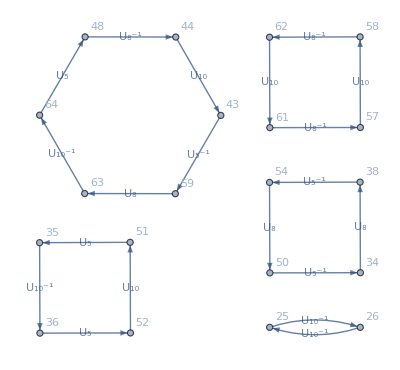

```mathematica
orderOfExpression[getExpression[412]]
Print[Dynamic[Plus@@Abs@exp]];
e=simplifyExpressionRandomly[getExpression[412],300000];
drawGraph[e]
```